```mathematica
Limit[Z1,{a->1.0}]
Limit[Z2,{a->1.0}]
Limit[ru,{a->1.0}]
Limit[lu,{a->1.0}]
Limit[e,{a->1.0}]
Limit[rl,{a->1.0}]
Limit[ll,{a->1.0}]
Limit[((1-2/r+a/r^(3/2))/(1-3/r+2 a/r^(3/2))^(1/2)//.{r->rl}),{a->1.0}]
```

{Z1}

{Z2}

{ru}

{lu}

{e}

{rl}

{ll}

{(1.-2. √rl+1. rl^(3/2))/(√(1.+2./rl^(3/2)-3./rl) rl^(3/2))}

```mathematica
Clear[a]
```

```mathematica
Z1 = 1 + (1 - a^2)^(1/3) ( (1 + a)^(1/3) + (1 - a)^(1/3) );

Z2 = Sqrt[ 3 a^2 + Z1^2 ];

ru = 3 + Z2 - Sqrt[ (3 - Z1)(3 + Z1 + 2 Z2) ];
rl = 3 + Z2 + Sqrt[ (3 - Z1)(3 + Z1 + 2 Z2) ];
myr=If[a>0,ru,rl];

l = ( Sqrt[r] (r^2 - 2 a Sqrt[r] + a^2))/(r (r^2 - 3 r + 2 a Sqrt[r])^(1/2) )//.{r->myr};

lu = ( Sqrt[r] (r^2 - 2 a Sqrt[r] + a^2))/(r (r^2 - 3 r + 2 a Sqrt[r])^(1/2) )//.{r->ru};
(* below mistake? *)
ll = ( Sqrt[rl] (rl^2 + 2 a Sqrt[rl] + a^2))/(rl (rl^2 - 3 rl - 2 a Sqrt[rl])^(1/2) );
ll2 = ( Sqrt[r] (r^2 - 2 a Sqrt[r] + a^2))/(r (r^2 - 3 r + 2 a Sqrt[r])^(1/2) )//.{r->rl};

e = ((1 - 2/r + a/r^(3/2))/(1 - 3/r + 2 a/r^(3/2))^(1/2) /. r -> myr);

eu = ((1 - 2/r + a/r^(3/2))/(1 - 3/r + 2 a/r^(3/2))^(1/2) /. r -> ru);
(* mistake vs. different form? *)
el = ((1 - 2/r + a/r^(3/2))/(1 - 3/r + 2 a/r^(3/2))^(1/2) /. r -> rl);

(* find coefficients in FE, FL, FM relation *)

W = 1/(ru^(3/2) + a);

coef = {W, e - lu W};
da=lu-2*a*e;
```

```mathematica
(* Newtonian Efficiency *)
Clear[G,M,c,r]
Solve[1/2*m*v^2==G*M*m/r,r]//.{v->c}
Solve[m*c^2==G*M*m/r,r]//.{v->c}
r=2*G*M/c^2
phi=G*M/r
Clear[G,M,c,r]
```

{{r→(2 G M)/c^2}}

{{r→(G M)/c^2}}

(2 G M)/c^2

c^2/2

```mathematica
omegak=1/(r^(3/2)+a)
rhor=1+Sqrt[1-a^2]
rergo=1+Sqrt[1-(a*Cos[h])^2]//.{h->Pi/2}
omegah=a/(2*rhor)

myomegah=omegah//.{a->0.9375}
myomegaf=myomegah/2
RA=1/myomegaf

omegakeqomegah=Solve[omegak==omegah,r][[1,1,2]]
omegakeqomegah=Solve[omegak==omegah,r][[1,1,2]]

myrl=rl//.{a->-j}//.{j->a};
myrisco=If[a<0,myrl,ru]
vk=1/(r^(3/2)+a)
vkatisco=vk//.{r->myrisco}
vbh=rhor*omegah/2
myomegakatrisco=Evaluate[omegak]//.{r->Evaluate[myrisco]}
```

1/(a+r^(3/2))

1+√(1-a^2)

2

a/(2 (1+√(1-a^2)))

0.347741

0.173871

5.7514

((2-a^2+2 √(1-a^2))/a)^(2/3)

((2-a^2+2 √(1-a^2))/a)^(2/3)

If[a<0,myrl,ru]

1/(a+r^(3/2))

1/(a+If[a<0,myrl,ru]^(3/2))

a/4

1/(a+If[a<0,myrl,ru]^(3/2))

```mathematica
nu=3/4
Rout=10^5.
```

3/4

100000.

```mathematica
nu=3/4
Rout=200
```

3/4

200

```mathematica
Rfp=1
Rint=Rfp*(Rout/Rfp)^((2-nu)/2)
Rtop=4*nu*Rint
gamma=Rtop/RA
gamma=Rint/RA
```

1

10 2^(7/8) 5^(1/4)

30 2^(7/8) 5^(1/4)

14.3051

4.76837

```mathematica
omegakeqomegah//.{a->.01}
```

54.2865

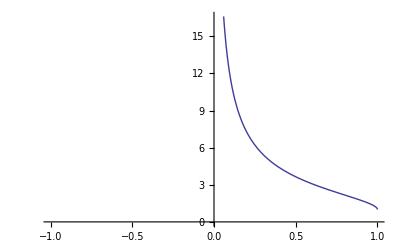

```mathematica
Plot[omegakeqomegah,{a,-1,1}]
```

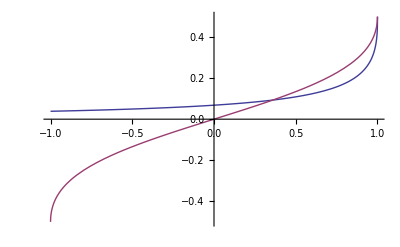

```mathematica
Plot[{myomegakatrisco,omegah},{a,-1,1}]
```

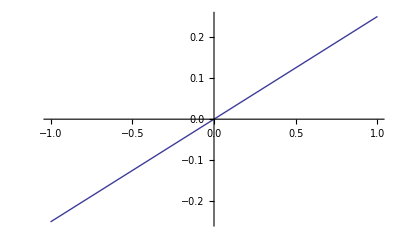

```mathematica
Plot[vbh,{a,-1,1}]
```

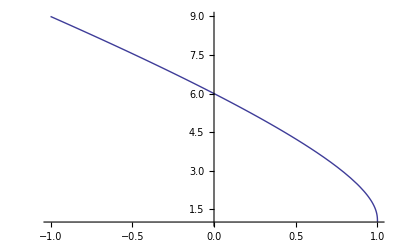

```mathematica
Plot[{myrisco},{a,-1,1}]
```

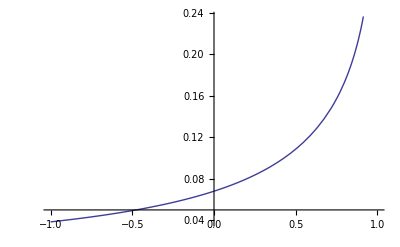

```mathematica
Plot[vkatisco,{a,-1,1}]
```

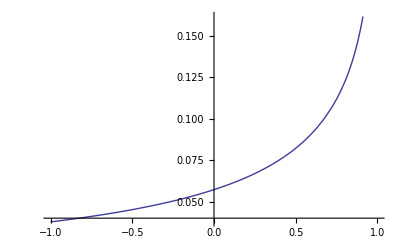

```mathematica
Plot[1-e,{a,-1,1}]
```

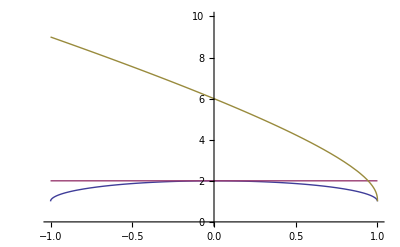

```mathematica
Plot[{rhor,rergo,myrisco},{a,-1,1},PlotRange->{0,10}]
```

```mathematica
FindRoot[myrisco==rergo,{a,.95}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {a} = {0.95}. Try perturbing the initial point(s).

{a→0.95}

```mathematica
myrisco
```

If[a<0,myrl,ru]

```mathematica
FindRoot[myrl==2,{a,0.95}]
FindRoot[ru==2,{a,0.95}]
```

Power::infy: Infinite expression 1/√0. encountered.

FindRoot::njnum: The Jacobian is not a matrix of numbers at {a} = {1.02866×10^-9}.

{a→1.02866×10^-9}

{a→0.942809}

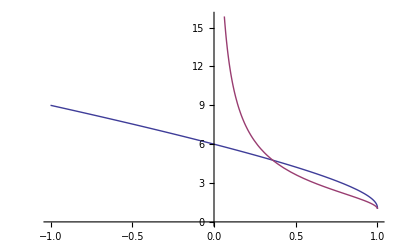

```mathematica
Plot[{myrisco,omegakeqomegah},{a,-1,1}]
```

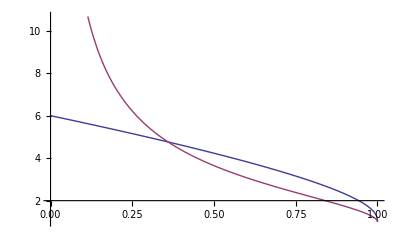

```mathematica
Plot[{ru,omegakeqomegah},{a,0,1}]
```

```mathematica
rl//.{a->-2.0}
ru//.{a->-2.0}
```

11.7026+8.88178×10^-16 ⅈ

-0.482982+3.08322 ⅈ

```mathematica
rl//.{a->2.0}
ru//.{a->2.0}
```

11.7026+8.88178×10^-16 ⅈ

-0.482982+3.08322 ⅈ

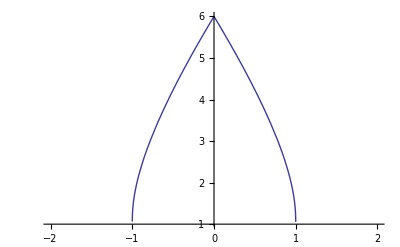

```mathematica
Plot[ru,{a,-2,2}]
```

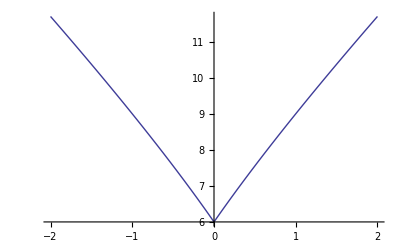

```mathematica
Plot[rl,{a,-2,2}]
```

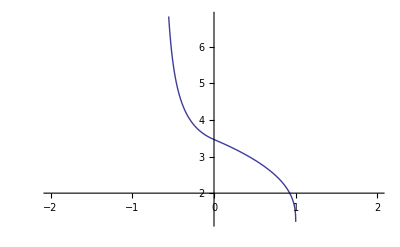

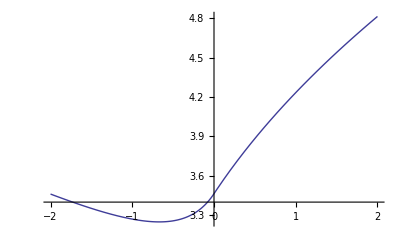

```mathematica
Plot[lu,{a,-2,2}]
Plot[ll,{a,-2,2}]
```

```mathematica
1-e//.{a->-0.99}
```

0.0378703

```mathematica
rp//.{a->-0.9}
```

rp

```mathematica
ru//.{a->-0.9}
rl//.{a->-0.9}
```

2.32088

8.71735

```mathematica
ll//.{a->-0.999999}
```

3.27052

```mathematica
1-el//.{a->-0.99999999999999999}
```

0.0377496

```mathematica
4.3372*0.961
```

4.16805

```mathematica
1-el//.{a->-0.9}
```

0.0389983

```mathematica
crap=0.9610
```

0.961

```mathematica
1-crap
```

0.039

```mathematica
rp=1+Sqrt[1-a^2]
omegah=a/(2*rp)
omegah1=omegah//.{a->1}
```

1+√(1-a^2)

a/(2 (1+√(1-a^2)))

1/2

```mathematica
badl=If[a>0,lu,ll]
```

If[a>0,lu,ll]

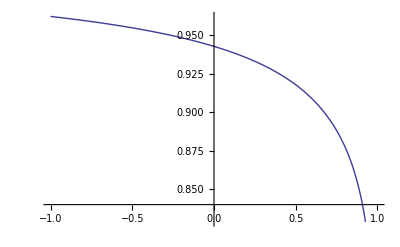

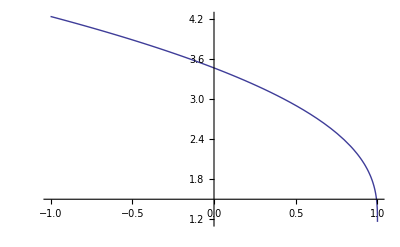

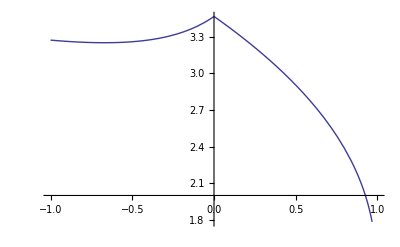

```mathematica
Plot[e,{a,-1,1}]
Plot[l,{a,-1,1}]
Plot[badl,{a,-1,1}]
```

```mathematica
CC=1-3/r+2*a/r^(3/2)
GG=1-2/r+a/r^(3/2)
nte=GG/CC^(1/2)
ntl=2/3^(1/2)/r^(1/2)*(3*r^(1/2)-2*a)
ntlisco=ntl//.{r->rl}//.{a->-0.9}
nteisco=nte//.{r->rl}//.{a->-0.90}
1-nteisco
```

1+(2 a)/r^(3/2)-3/r

1+a/r^(3/2)-2/r

(1+a/r^(3/2)-2/r)/(√(1+(2 a)/r^(3/2)-3/r))

(2 (-2 a+3 √r))/(√3 √r)

4.16806

0.961002

0.0389983

```mathematica
l//.{a->-0.9}
```

4.16806

```mathematica
1-e//.{a->-.90000}
```

0.0389983

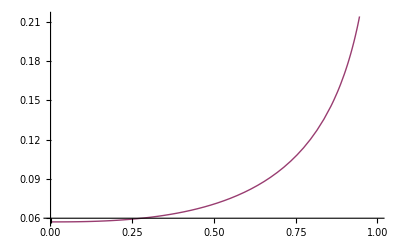

```mathematica
Plot[{1-mye,0.0572+(0.422644-0.0572)*(omegah/omegah1)^2.5},{a,0,1}]
```

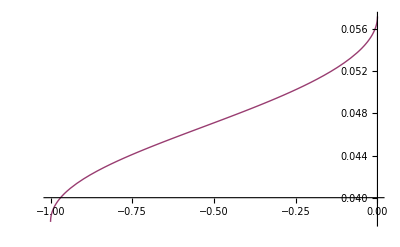

```mathematica
Plot[{1-mye,0.0572+(0.0377-0.0572)*(-omegah/omegah1)^.5},{a,-1,0}]
```

```mathematica
rp=1+Sqrt[1-a^2]
omegah=a/(2*rp)
omegak=1/(r^(3/2)+a)
```

1+√(1-a^2)

a/(2 (1+√(1-a^2)))

1/(a+r^(3/2))

```mathematica
fun=(omegak//.{r->ru})==omegah;
FindRoot[fun,{a,0.5}]
```

{a→0.359403}

```mathematica
lu//.{a->0.9}
```

2.09978

```mathematica
e//.{a->0.9}
```

0.844247

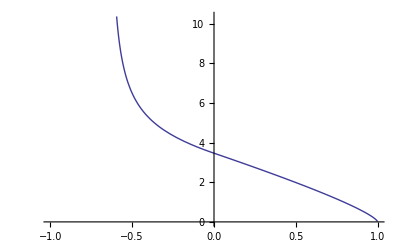

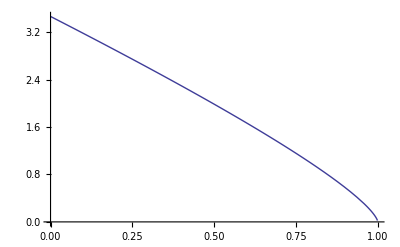

```mathematica
Plot[da,{a,-.999,.999}]
Plot[da,{a,0,.999}]
```

```mathematica
(*Limit[da,{a->1}]*)
```

```mathematica
dan=N[da//.{a->jj/100}];
```

```mathematica
bardeenj=Table[jj/100.,{jj,0,99}];
```

```mathematica
bardeendjdt=Table[dan,{jj,0,99}];
```

```mathematica
bardeenj
bardeendjdt
```

{0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99}

{3.4641,«98»,1.56836-(1.98 (1.+0.99/(«1»)-2./(3+√(«1»)-√(«1»))))/(√(1.+1.98/(«1»)^(«1»)-3./(3+«1»-«1»)))}

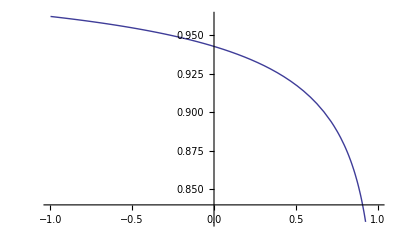

```mathematica
Plot[e,{a,-.999,.999}]
```

```mathematica
e
```

(1+a/If[a>0,ru,rl]^(3/2)-2/If[a>0,ru,rl])/(√(1+(2 a)/If[a>0,ru,rl]^(3/2)-3/If[a>0,ru,rl]))

```mathematica
e=((1-2/r+a/r^(3/2))/(1-3/r+2 a/r^(3/2))^(1/2)/.r->rl)
```

(1+a/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)-2/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))))/(√(1+(2 a)/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)-3/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))))

```mathematica
Clear[a]
```

```mathematica
mya={-0.938, 0.0,.05, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.4, 0.5, 0.6, 0.75, 0.875, 0.895, 0.9 ,0.938, 0.969}
adotomdot={-5.583,-3.049,-2.921,-2.713,-2.597,-2.439,-2.302,-2.217,-1.975,-1.986,-1.665,-1.347,-0.808,-0.152,-0.204,-0.118, 0.067, 0.217}
```

{-0.938,0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.875,0.895,0.9,0.938,0.969}

{-5.583,-3.049,-2.921,-2.713,-2.597,-2.439,-2.302,-2.217,-1.975,-1.986,-1.665,-1.347,-0.808,-0.152,-0.204,-0.118,0.067,0.217}

```mathematica
adotomdotvsa=Table[{mya[[i]],-adotomdot[[i]]},{i,1,18}]
```

{{-0.938,5.583},{0.,3.049},{0.05,2.921},{0.1,2.713},{0.15,2.597},{0.2,2.439},{0.25,2.302},{0.3,2.217},{0.35,1.975},{0.4,1.986},{0.5,1.665},{0.6,1.347},{0.75,0.808},{0.875,0.152},{0.895,0.204},{0.9,0.118},{0.938,-0.067},{0.969,-0.217}}

```mathematica
a2={-0.938, 0.0, .05, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.4, 0.5, 0.6, 0.75, 0.875, .895, .9 , 0.938, 0.969}
jdot= {5.583, 3.049, 2.921, 2.713, 2.597, 2.439, 2.302, 2.217, 1.975, 1.986, 1.665, 1.347, 0.808, 0.152, 0.204, 0.118, -0.067, -0.217}
hor={0.211,0.266,0.280,0.280,0.299,0.308,0.323,0.253,0.261,0.185,0.204,0.220,0.248,0.261,0.266,0.261,0.270,0.270}
```

{-0.938,0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.875,0.895,0.9,0.938,0.969}

{5.583,3.049,2.921,2.713,2.597,2.439,2.302,2.217,1.975,1.986,1.665,1.347,0.808,0.152,0.204,0.118,-0.067,-0.217}

{0.211,0.266,0.28,0.28,0.299,0.308,0.323,0.253,0.261,0.185,0.204,0.22,0.248,0.261,0.266,0.261,0.27,0.27}

```mathematica
myjdot=Table[{a2[[i]],jdot[[i]]},{i,1,18}]
myhor=Table[{a2[[i]],hor[[i]]},{i,1,18}]
```

{{-0.938,5.583},{0.,3.049},{0.05,2.921},{0.1,2.713},{0.15,2.597},{0.2,2.439},{0.25,2.302},{0.3,2.217},{0.35,1.975},{0.4,1.986},{0.5,1.665},{0.6,1.347},{0.75,0.808},{0.875,0.152},{0.895,0.204},{0.9,0.118},{0.938,-0.067},{0.969,-0.217}}

{{-0.938,0.211},{0.,0.266},{0.05,0.28},{0.1,0.28},{0.15,0.299},{0.2,0.308},{0.25,0.323},{0.3,0.253},{0.35,0.261},{0.4,0.185},{0.5,0.204},{0.6,0.22},{0.75,0.248},{0.875,0.261},{0.895,0.266},{0.9,0.261},{0.938,0.27},{0.969,0.27}}

```mathematica
mythinjdot=Table[da//.{a->a2[[i]]},{i,1,18}]
```

{1.80375-2.51023 ⅈ,3.4641,3.32219,3.17924,3.03517,2.88988,2.74327,2.59521,2.44555,2.29411,1.98498,1.66544,1.15715,0.684885,0.601515,0.58014,0.408228,0.247391}

```mathematica
thickhor=Table[{a2[[i]],hor[[i]]},{i,2,18}]
thinjdot=Table[{a2[[i]],da//.{a->a2[[i]]}},{i,2,18}]
thickjdot=Table[{a2[[i]],jdot[[i]]},{i,2,18}]
```

{{0.,0.266},{0.05,0.28},{0.1,0.28},{0.15,0.299},{0.2,0.308},{0.25,0.323},{0.3,0.253},{0.35,0.261},{0.4,0.185},{0.5,0.204},{0.6,0.22},{0.75,0.248},{0.875,0.261},{0.895,0.266},{0.9,0.261},{0.938,0.27},{0.969,0.27}}

{{0.,3.4641},{0.05,3.32219},{0.1,3.17924},{0.15,3.03517},{0.2,2.88988},{0.25,2.74327},{0.3,2.59521},{0.35,2.44555},{0.4,2.29411},{0.5,1.98498},{0.6,1.66544},{0.75,1.15715},{0.875,0.684885},{0.895,0.601515},{0.9,0.58014},{0.938,0.408228},{0.969,0.247391}}

{{0.,3.049},{0.05,2.921},{0.1,2.713},{0.15,2.597},{0.2,2.439},{0.25,2.302},{0.3,2.217},{0.35,1.975},{0.4,1.986},{0.5,1.665},{0.6,1.347},{0.75,0.808},{0.875,0.152},{0.895,0.204},{0.9,0.118},{0.938,-0.067},{0.969,-0.217}}

```mathematica
diffjdot=Table[{a2[[i]],jdot[[i]]-((da//.{a->a2[[i]]})-0.395)},{i,2,18}]
```

{{0.,-0.0201016},{0.05,-0.00618732},{0.1,-0.0712368},{0.15,-0.0431669},{0.2,-0.0558824},{0.25,-0.0462737},{0.3,0.0167867},{0.35,-0.0755513},{0.4,0.0868901},{0.5,0.0750159},{0.6,0.0765578},{0.75,0.0458549},{0.875,-0.137885},{0.895,-0.00251485},{0.9,-0.0671401},{0.938,-0.080228},{0.969,-0.0693909}}

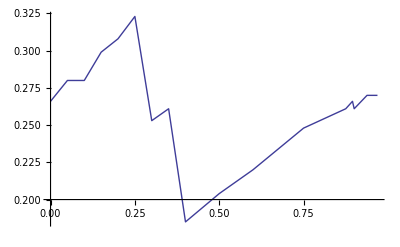

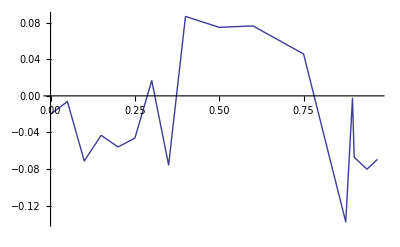

```mathematica
q0=ListPlot[thickhor,PlotJoined->True]
q1=ListPlot[diffjdot,PlotJoined->True]
```

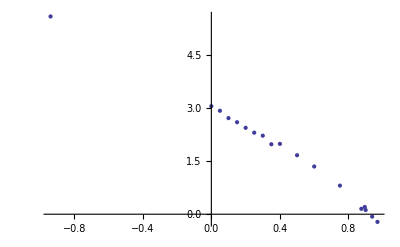

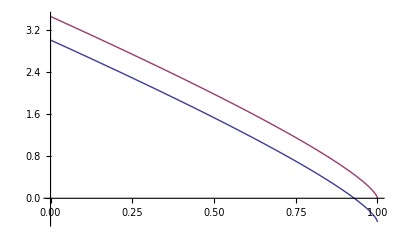

3.55-3.28 a

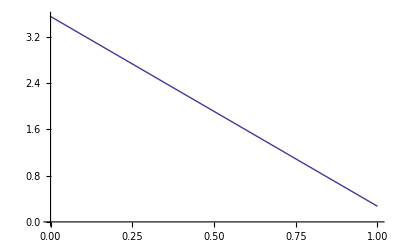

3.14-3.31 a

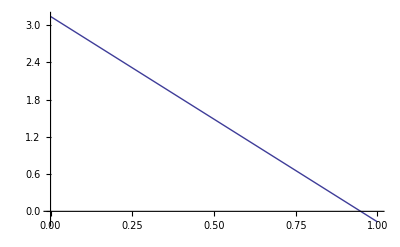

3.05-2.7 a

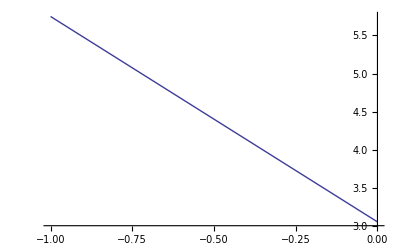

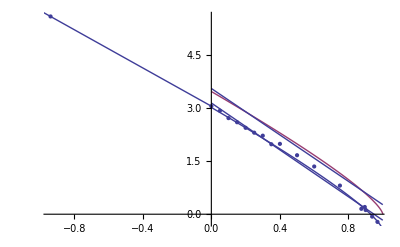

```mathematica
p1=ListPlot[adotomdotvsa]
p2=Plot[{da-0.45,da},{a,0,1}]
fitda=-3.28*a+3.55
p22=Plot[fitda,{a,0,1}]
fitgreaterda=-3.31*a+3.14
p3=Plot[fitgreaterda,{a,0,1}]
fitlessda=-2.7*a+3.05
p4=Plot[fitlessda,{a,-1,0}]
Show[{p1,p2,p22,p3,p4}]
```

```mathematica
(* other analysis related to GRB stuff *)
```

```mathematica
da0=da//.{a->0.}
da1=da//.{a->.99999}
dada=(da1-da0)/.99999
myda=da0+dada*a
jonda=1.65+(-.2-1.65)/(.968-0.5)*(a-0.5)
```

3.4641

0.0010217

-3.46311

3.4641-3.46311 a

1.65-3.95299 (-0.5+a)

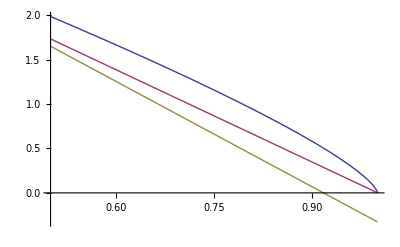

```mathematica
Plot[{da,myda,jonda},{a,0.5,1}]
```

```mathematica
jongrbdavert=2.8*10^(-7)*jonda//.{a->j[t]}
jongrbdafid=1.4*10^(-6)*jonda//.{a->j[t]}
tdgrbda=2.8*10^(-7)*da//.{a->j[t]};
```

2.8×10^-7 (1.65-3.95299 (-0.5+j[t]))

1.4×10^-6 (1.65-3.95299 (-0.5+j[t]))

```mathematica
Clear[j]
```

```mathematica
jonavstvert=NDSolve[{jongrbdavert==j'[t],j[0]==0.75},j,{t,0,2.7*10^7}]
jonavstfid=NDSolve[{jongrbdafid==j'[t],j[0]==0.75},j,{t,0,2.7*10^7}]
tdavst=NDSolve[{tdgrbda==j'[t],j[0]==0.855},j,{t,0,2.7*10^7}]
```

{{j→InterpolatingFunction[{{0.,2.7×10^7}},<>]}}

{{j→InterpolatingFunction[{{0.,2.7×10^7}},<>]}}

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{2.8×10^-7 (-(2 j[t] (1-2/If[j[t]>0,ru,rl]+j[t]/If[j[t]>0,ru,rl]^(3/2)))/(√(1-3/If[j[t]>0,ru,rl]+(2 j[t])/If[j[t]>0,ru,rl]^(3/2)))+(j[t]^2-2 j[t] √(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))+(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))^2)/(√(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)))) √(2 j[t] √(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))-3 (3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))+(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))^2)))==j'[t],j[0]==0.855},j,{t,0,2.7×10^7}]

```mathematica
j[1.35*10^6/20*18.5]/.jonavstvert
j[1.35*10^6/20*18.5]/.jonavstfid
j[1.35*10^6/20*18.5]/.tdavst
```

{0.875381}

{0.917239}

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

j[1.24875×10^6]/.NDSolve[{2.8×10^-7 (-(2 j[t] (1-2/If[j[t]>0,ru,rl]+j[t]/If[j[t]>0,ru,rl]^(3/2)))/(√(1-3/If[j[t]>0,ru,rl]+(2 j[t])/If[j[t]>0,ru,rl]^(3/2)))+(j[t]^2-2 j[t] √(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))+(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))^2)/(√(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)))) √(2 j[t] √(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))-3 (3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))+(3+√(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2)-√((2-(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))) (4+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3))+2 √(3 j[t]^2+(1+(1-j[t]^2)^(1/3) ((1-j[t])^(1/3)+(1+j[t])^(1/3)))^2))))^2)))==j'[t],j[0]==0.855},j,{t,0,2.7×10^7}]

```mathematica
j[3.35*10^7/20*18.5]/.jonavstvert
j[3.35*10^7/20*18.5]/.jonavstfid
```

InterpolatingFunction::dmval: Input value {3.09875×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.917405}

InterpolatingFunction::dmval: Input value {3.09875×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.917405}

```mathematica
Plot[j[t]/.jonavst,{t,0,1.35*10^6}]
```

ReplaceAll::reps: {jonavst} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{j[t]/.tdavst,j[t]/.jonavst},{t,0,1.35*10^6}]
```

NDSolve::dsvar: 27.5786 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 27.5786 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 27578.6 cannot be used as a variable.

General::stop: Further output of NDSolve :: "dsvar" will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

-Graphics-

```mathematica
jonda//.{a->0.5}
```

1.65

```mathematica
1-e
```

1-(1+a/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)-2/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))))/(√(1+(2 a)/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)-3/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))))

```mathematica
rp=1+Sqrt[1-a^2]
wh=a/(2*rp)
rat=W/wh
```

1+√(1-a^2)

a/(2 (1+√(1-a^2)))

(2 (1+√(1-a^2)))/(a (a+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)))

```mathematica
(* for a=0.9375 *)
```

```mathematica
f23gammie=0.63*0.942*Sqrt[.17*1.35]/(2*Pi)
```

0.0452484

```mathematica
lu
```

(a^2-2 a √(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^2)/(√(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))) √(2 a √(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))-3 (3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^2))

```mathematica
1.-e
```

1.-(1+a/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)-2/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))))/(√(1+(2 a)/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^(3/2)-3/(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)+√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))))

```mathematica
1+Sqrt[1-a^2]
```

1+√(1-a^2)

```mathematica
lu
```

(a^2-2 a √(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^2)/(√(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))) √(2 a √(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))-3 (3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^2))

```mathematica
0.18*.268/(6*10^(-3))
```

8.04

```mathematica
Clear[rp,a]
```

1-√(1-a^2)

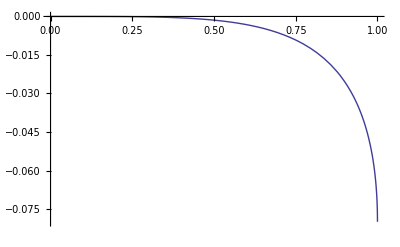

```mathematica
rp=1-Sqrt[1-a^2]
Plot[-.08*rp^2,{a,0,1},PlotRange->{-.08,0}]
```